```mathematica
first = Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1, {1,2,3,4}}]
```

{{Fe-Ni,,,Fe-Si,,,Ferrit,,,tau,,},{2X_s,5.2,50 мВ,2X_s,,0,1 В,2X_s,,20 мВ,U  вых,0.066,В},{2Y_s,4.6,0,1 В,2Y_s,,0,1 В,2Y_s,,20 мВ,U  вх,8.,В},{,,,,,,,,,,,}}

```mathematica
TableForm[first]
```

Fe-Ni |  |  | Fe-Si |  |  | Ferrit |  |  | tau |  | 
2X_s | 5.2 | 50 мВ | 2X_s |  | 0,1 В | 2X_s |  | 20 мВ | U  вых | 0.066 | В
2Y_s | 4.6 | 0,1 В | 2Y_s |  | 0,1 В | 2Y_s |  | 20 мВ | U  вх | 8. | В
 |  |  |  |  |  |  |  |  |  |  |

```mathematica
TableForm[%6]
```

Fe-Ni |  |  | Fe-Si |  |  | Ferrit |  |  | tau |  | 
2X_s | 5.2 | 50 мВ | 2X_s |  | 0,1 В | 2X_s |  | 20 мВ | U  вых | 0.066 | В
2Y_s | 4.6 | 0,1 В | 2Y_s |  | 0,1 В | 2Y_s |  | 20 мВ | U  вх | 8. | В
 |  |  |  |  |  |  |  |  |  |  |

```mathematica
Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1}]
```

{{Fe-Ni,,,Fe-Si,,,Ferrit,,,tau,,},{2X_s,5.2,50 мВ,2X_s,,0,1 В,2X_s,,20 мВ,U  вых,0.066,В},{2Y_s,4.6,0,1 В,2Y_s,,0,1 В,2Y_s,,20 мВ,U  вх,8.,В},{,,,,,,,,,,,},{2X_c,2.4,,2X_c,,,2X_c,,,nu,50.,Гц},{2Y_r,4.4,,2Y_r,,,2Y_r,,,tau,0.386026,с},{,,,,,,,,,tau_0,0.4,с},{Цена деления,,,,,,,,,,,},{H,7.29167,А/м,,,,,,,,,},{B,0.478469,Тл,,,,,,,,,},{,,,,,,,,,,,},{X,Y,,,,,,,,,,},{2.,2.2,,,,,,,,,,},{1.8,2.1,,,,,,,,,,},{1.6,2.05,,,,,,,,,,},{1.4,2.,,,,,,,,,,},{1.2,1.9,,,,,,,,,,},{1.,1.7,,,,,,,,,,},{0.8,1.1,,,,,,,,,,},{0.6,0.4,,,,,,,,,,},{0.4,0.1,,,,,,,,,,},{0.,0.,,,,,,,,,,}}

```mathematica
Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1, Range[13,22],  {1,2}}]
```

{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}

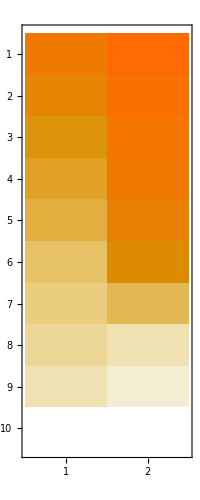

```mathematica
MatrixPlot[{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}]
```

```mathematica
Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1, Range[13,22],  {1,2}}]
```

{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}

```mathematica
TableForm[{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}]
```

2. | 2.2
1.8 | 2.1
1.6 | 2.05
1.4 | 2.
1.2 | 1.9
1. | 1.7
0.8 | 1.1
0.6 | 0.4
0.4 | 0.1
0. | 0.

{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}

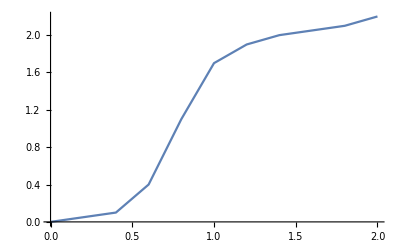

```mathematica
a = Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1, Range[13,22],  {1,2}}]
ListLinePlot[a]
```

```mathematica
Show[%18,Axes->True]
```

-Graphics-

```mathematica
Import["/Users/kekoveca/Documents/MIPT/physics/2 course/lab345/lab345.xlsx", {"Data", 1, Range[13,22],  {1,2}}]
```

{{2.,2.2},{1.8,2.1},{1.6,2.05},{1.4,2.},{1.2,1.9},{1.,1.7},{0.8,1.1},{0.6,0.4},{0.4,0.1},{0.,0.}}

```mathematica
ListLinePlot[a]
```

-Graphics-

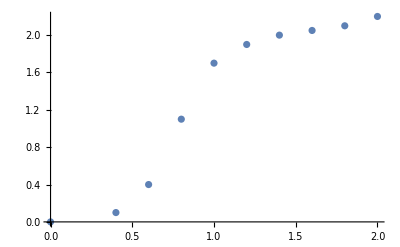

```mathematica
ListPlot[a]
```

```mathematica
line = Fit[a, {1, x, x^2, x^3, x^4, x^5}, x]
```

0.0068696-2.87989 x+9.64904 x^2-6.28899 x^3+0.971072 x^4+0.129619 x^5

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

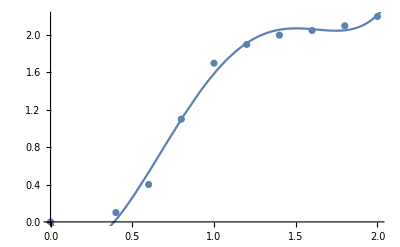

```mathematica
Show[ListPlot[a], Plot[line, {x, 0, 5}]]
```

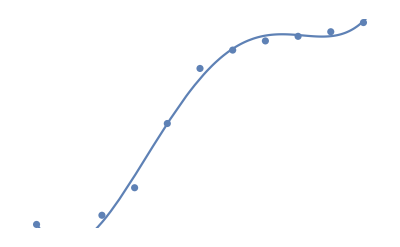

```mathematica
Show[%42,Axes->False]
```